```mathematica
(*Proyecto del modelo poblacional de Lotka-Volterra*)
(*Integrantes: Calvo Ramos Daniel Farid
			 Chuzeville Rosas Catherine Etienne
			 Santos Barbosa José Emmanuel*)
```

```mathematica
(*Aquí se prueba el comando "NDSolveValue" para el sistema Lotka-Volterra*)
δ = γ = σ = 0.1;
(*En este caso, se resolvio el conjunto de ecuaciones para un tiempo de 0 a 100, utilizando α=3 y β=2.*)
{solx, soly}=NDSolveValue[{x'[t]== 3 x[t]-2 x[t] y[t],y'[t]== δ x[t] y[t]-γ y[t]+σ Sin[t],x[0]==1,y[0]==1},{x,y},{t,100}]
(*Arrojando como resultado una función que interpola para el eje x y el eje y.*)
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
(*Aquí se grafican las funciones de las soluciones por separado, se puede apreciar que conforme pasa el tiempo, ambas son periodicas y estables. *)
Plot[{solx[t],soly[t]},{t,0,25},Frame->{True,True,False,False},FrameLabel->{"Eje t","f(t)"},LabelStyle->Directive[Black,Bold],PlotLabel->Style["Soluciones del sistema para x e y",FontSize->12],PlotLabels->{"Función para x(t)","Función para y(t)"},PlotStyle->{Red,Orange},PlotRange->All]
```

-Graphics-

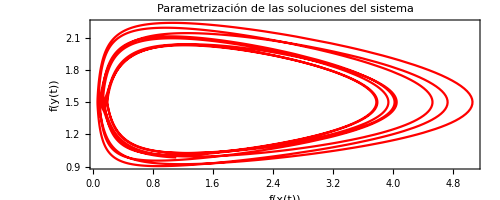

```mathematica
(*Se grafican ambas funciones dependientes del parametro t en un mismo plano, donde se aprecia la estabilidad y periodicidad del sistema*)
ParametricPlot[{solx[t],soly[t]},{t,0,100},Frame->{True,True,False,False},FrameLabel->{"f(x(t))","f(y(t))"},LabelStyle->Directive[Black,Bold],PlotLabel->Style["Parametrización de las soluciones del sistema",FontSize->12],PlotStyle->Red,PlotRange->All]
```

```mathematica
(*Resolviendo ahora el sistema bajo condiciones iniciales arbitrarias para calcular el exponente de Lyapunov.*)
```

```mathematica
SolveWithInitial[xInitial_,yInitial_,tMax_]:=Block[{δ = 0.1, γ = 0.1, σ = 0.1, x,y},
NDSolveValue[
{x'[t]== 3 x[t]-2 x[t] y[t],y'[t]== δ x[t] y[t]-γ y[t]+σ Sin[t], x[0] == xInitial ,  y[0] == yInitial},
{x,y},
{t,0,tMax},AccuracyGoal->40,MaxSteps->10^6
]
];
```

```mathematica
(*Aquí algunos ejemplos de la función que resuelve el sistema bajo condiciones arbitrarias*)
```

```mathematica
SolveWithInitial[6,1,200]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

```mathematica
Last[SolveWithInitial[6,1,200]]
```

InterpolatingFunction[…]

```mathematica
(*En esta parte se calcula el exponente de Lyapunov para el sistema Lotka-Volterra.*)
CalculateLyapunov[f_,xMin_,xMax_,Δx_]:=Block[{lyapunovPoints},
lyapunovPoints = DeleteCases[Table[Log[Abs[f'[t]]],{t,xMin,xMax,Δx}],Indeterminate];
Total[lyapunovPoints]/Length[lyapunovPoints]
];
```

```mathematica
(*Aquí un ejemplo de la función que calcula el exponente de Lyapunov aplicado a la solución de y con yInitial=1 y con un tiempo que va de 0 a 200 con un intervalo de 0.01.*)
```

```mathematica
CalculateLyapunov[InterpolatingFunction[…],0,200,0.01]
```

-2.07637

```mathematica
Needs["AdvancedMapping`"]
```

```mathematica
(*Finalmente aquí se grafica el exponente de Lyapunov para diferentes valores de x e y, en donde se aprecian las zonas estables del sistema (en azul) y las zonas caoticas (en café).*)
λs = Flatten[
Quiet@ProgressTable[
If[xInitial ≠ yInitial,
{xInitial,yInitial,CalculateLyapunov[Last[SolveWithInitial[xInitial,yInitial,100]],0,99,0.1]},
Nothing
],
{xInitial,0.1,3,0.01},{yInitial,0.1,2,0.01}
],
1
];
```

$Aborted

```mathematica
ListContourPlot[λs,InterpolationOrder->0,PlotLegends->Automatic]
```

-Graphics-